```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Directory[]
Off[Needs::nocont];Needs["LowDiscrep`"];
On[Needs::nocont];
SeedRandom[1234];
```

/Users/npadmana/myWork/lowdiscrepancyRR/mma

## Timing of LDS generation

```mathematica
Timing[generateLDSshiftedGrid[100^2,6];]
```

{0.004698,Null}

```mathematica
Timing[generateLDSshiftedGrid[1000^2,6];]
```

{0.496343,Null}

```mathematica
Timing[generateLDSshiftedGrid[2000^2,6];]
```

{2.21934,Null}

## 3D shell function

y = r^3/3, x = (r^3- r_1^3)/(r_2^3- r_1^3)

```mathematica
Clear[shellFunc];
shellFunc[rlo_, rhi_]:= Compile[{{x,_Real,1}},
Module[{r, cth,sth, ϕ, x1, y1, z1, jac},
ϕ = x[[6]]*2π;
cth = x[[5]]*2.0-1.0;
sth = Sqrt[1-cth^2];
r = (x[[4]]*(rhi^3- rlo^3)+ rlo^3)^(1/3);
x1 = x[[1]]+r*sth*Cos[ϕ];
y1 = x[[2]]+r*sth*Sin[ϕ];
z1 = x[[3]]+r*cth;
If[(x1 >0)&&(x1 < 1) && (y1 > 0) && (y1 < 1) && (z1 >0) && (z1 <1), 1.0, 0.0]
],
CompilationTarget->"C", 
RuntimeAttributes->{Listable}];
```

```mathematica
shellFuncJac[rlo_, rhi_]:= 4π (rhi^3- rlo^3)/3;
```

```mathematica
rr3dbin[rlo_, rhi_, num_]:= mcIntegrate[shellFunc[rlo,rhi],generateLDSshiftedGrid[num, 6]]*shellFuncJac[rlo,rhi];
```

```mathematica
Timing[rr3dbin[0.25,0.5,100000]]
```

{0.23168,0.227558}

```mathematica
Timing[rr3dbin[0.25,0.5,1000000]]
```

{1.29793,0.227832}

## Histograms

```mathematica
Timing[v1 = Reap[Do[Sow[rr3dbin[0.25, 0.5, 10000]],{1000}]][[2,1]];]
```

{139.984,Null}

```mathematica
Mean[v1]
```

0.227942

```mathematica
StandardDeviation[v1]/Mean[v1]
```

0.00526562

```mathematica
(* Histogram for 10000 pts *)
```

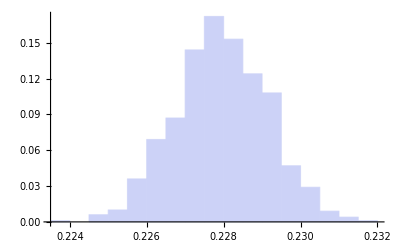

```mathematica
Histogram[v1,{0.0005}, "Probability"]
```

```mathematica
Timing[v2 = Reap[Do[Sow[rr3dbin[0.25, 0.5, 100000]],{1000}]][[2,1]];]
```

{234.791,Null}

```mathematica
Mean[v2]
```

0.227911

```mathematica
StandardDeviation[v2]/Mean[v2]
```

0.00114004

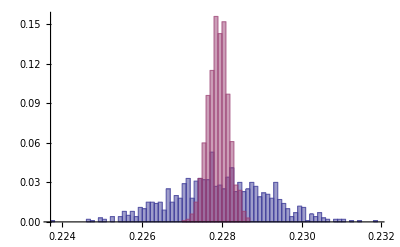

```mathematica
Histogram[{v1,v2},{0.0001}, "Probability"]
```

## Error Scaling

```mathematica
nvals = {1,2,5,10,20,50,100}*10000;
```

```mathematica
Timing[lds1=Table[getmeanerror[rr3dbin[0.25, 0.5, ii], 100], {ii, nvals}];]
```

{283.394,Null}

```mathematica
lds1
```

{{0.228063,0.00128296},{0.227853,0.000848144},{0.227915,0.000481742},{0.227873,0.000238015},{0.227935,0.000150748},{0.227918,0.0000806865},{0.227892,0.0000492241}}

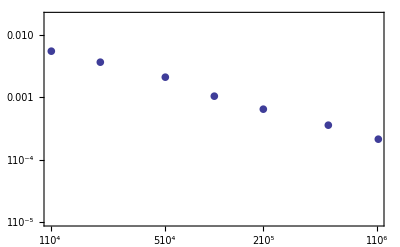

```mathematica
ListLogLogPlot[Transpose[{nvals, lds1[[All,2]]/lds1[[7,1]]}],  Frame->True, PlotMarkers->{Automatic, 10}, PlotRange->{Automatic, {1.*^-5, 0.02}}]
```

```mathematica
Fit[Log[Transpose[{nvals,  lds1[[All,2]]}]],{1,x},x]
```

0.0533699-0.72254 x

## All together now!

```mathematica
rbins = {0.015625,0.03125,0.0625,0.125,0.25,0.5};
```

```mathematica
nrbins = Dimensions[rbins][[1]]
```

6

```mathematica
Timing[lds=Table[getmeanerror[rr3dbin[rbins[[ir]], rbins[[ir+1]], ii], 100], {ir, nrbins-1},{ii, nvals}];]
```

{1431.69,Null}

```mathematica
Dimensions[lds]
```

{5,7,2}

```mathematica
(* Calculated values for all the bins *)
```

```mathematica
Transpose[{Drop[rbins,-1],lds[[All, 7, 1]]}]//TableForm
```

0.015625 | 0.000107686
0.03125 | 0.00082888
0.0625 | 0.00612673
0.125 | 0.0414849
0.25 | 0.2279

```mathematica
(* Fits *) 
fits = Table[Fit[Log[Transpose[{nvals, lds[[ii, All, 2]]}]],{1,x},x],{ii, 5}]
```

{-9.68092-0.686197 x,-7.65715-0.660562 x,-4.85609-0.700444 x,-2.8104-0.675696 x,-0.200489-0.698885 x}

```mathematica
Export["rr3d.h5", {rbins, lds},{"Datasets",{"rbins", "lds"}}];
```

```mathematica
Import["rr3d.h5"]
```

{/lds,/rbins}

```mathematica
inp = Import["rr3d.h5", {"Datasets",{"rbins","lds"}}];
```

```mathematica
inp
```

{{0.015625,0.03125,0.0625,0.125,0.25,0.5},{{{0.000107673,1.05773×10^-7},{0.000107693,7.22427×10^-8},{0.000107685,3.75898×10^-8},{0.000107682,2.26882×10^-8},{0.000107683,1.60017×10^-8},{0.000107685,7.66645×10^-9},{0.000107686,4.46386×10^-9}},{{0.000828864,1.00973×10^-6},{0.000828931,7.00464×10^-7},{0.000828905,4.00981×10^-7},{0.000828851,2.25351×10^-7},{0.000828886,1.55512×10^-7},{0.000828882,8.08039×10^-8},{0.00082888,4.98136×10^-8}},{{0.00612424,0.0000115477},{0.0061273,7.27012×10^-6},{0.00612655,4.61546×10^-6},{0.00612643,2.43951×10^-6},{0.00612639,1.50502×10^-6},{0.00612669,7.92611×10^-7},{0.00612673,4.67191×10^-7}},{{0.0414729,0.0000987315},{0.0414924,0.0000839431},{0.0414809,0.0000458319},{0.0414834,0.0000245906},{0.0414842,0.000017227},{0.0414828,7.71958×10^-6},{0.0414849,5.16059×10^-6}},{{0.227957,0.00115843},{0.227803,0.000860971},{0.227872,0.000493906},{0.227915,0.000251441},{0.227891,0.000159241},{0.227911,0.0000835316},{0.2279,0.0000516035}}}}

```mathematica
Dimensions[inp[[2]]]
```

{5,7,2}

```mathematica
plotlist = Table[Transpose[{nvals, lds[[ii, All,2]]/lds[[ii, 7,1]]}], {ii, 5}];
```

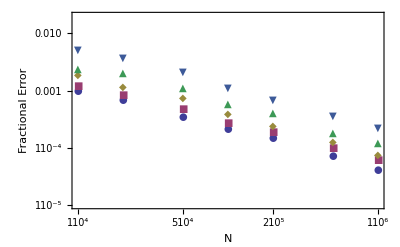

```mathematica
ListLogLogPlot[plotlist,Frame->True, PlotMarkers->{Automatic, 10}, PlotRange->{Automatic, {1.*^-5, 0.02}}, FrameLabel->{"N", "Fractional Error"}]
```